Total ask vol:1394

Total bid vol:1440

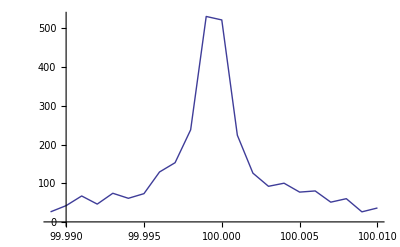

```mathematica
ClearAll[startAsk, startBid,tick, noOfOrders ,generateOrder, orders, cumVol];

tick = 0.001;
startAsk = 100;
startBid = startAsk-tick;
noOfOrders = 1000;

generateOrder[startBid_,startAsk_, tick_ ] := Module[{side, size, ticks, price},
side = RandomVariate[BernoulliDistribution[0.5]]; (*0-bid, 1-ask*)
ticks=RandomVariate[PowerDistribution[100,0.3]];
size = Round[RandomVariate[LogNormalDistribution[1,0.3] ]];
price =If[side == 1, startAsk+ticks ,startBid-ticks]; 
{Round[price,tick],size, side}
];

orders =Sort[ Table[generateOrder[startBid, startAsk, 0.001], {noOfOrders }],#[[1]]>#2[[1]]&];
cumVol={#[[1]][[1]],Total[#[[2]]&/@#]}&/@GatherBy[orders,#[[1]]&];
Print["Total ask vol:"<>ToString[Total[#[[2]]&/@Select[orders,#[[3]]==1&]]]];
Print["Total bid vol:"<>ToString[Total[#[[2]]&/@Select[orders,#[[3]]==0&]]]];
Print[Show[ListLinePlot[cumVol]]];
Export["/Users/jakubkozlowski/Desktop/orders.csv",orders];
```